## Matrix product operators for the Bose-Hubbard model

References:
	F. Verstraete, V. Murg, J. I. Cirac
	Matrix product states, projected entangled pair states, and variational renormalization group methods for quantum spin systems
	Advances in Physics 57, 143-224 (2008) DOI

	Thomas Barthel
	Precise evaluation of thermal response functions by optimized density matrix renormalization group schemes
	New Journal of Physics 15, 073010 (2013) DOI

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<tn_base.m
```

### Construct full Hamiltonian as reference

```mathematica
SparseIdentityMatrix[d_]:=SparseArray[{i_,i_}->1,{d,d}]
```

```mathematica
SiteCreateOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],-1]
SiteAnnihilOp[M_]:=DiagonalMatrix[Sqrt[Range[1,M]],1]
```

```mathematica
NumberOp[M_]:=DiagonalMatrix[Range[0,M]]
```

```mathematica
Comm[A_,B_]:=A.B-B.A
```

```mathematica
(* example *)
SiteCreateOp[5]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | √2 | 0 | 0 | 0 | 0
0 | 0 | √3 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | √5 | 0)

```mathematica
(* example *)
SiteAnnihilOp[5]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0
0 | 0 | √2 | 0 | 0 | 0
0 | 0 | 0 | √3 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | √5
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(* example: number operator *)
NumberOp[5]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 4 | 0
0 | 0 | 0 | 0 | 0 | 5)

```mathematica
NumberOp[5].(NumberOp[5]-IdentityMatrix[6])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 0
0 | 0 | 0 | 0 | 12 | 0
0 | 0 | 0 | 0 | 0 | 20)

```mathematica
(* last entry not 1 due to cut-off *)
Comm[SiteAnnihilOp[4],SiteCreateOp[4]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | -4)

```mathematica
(* check *)
Table[Norm[NumberOp[M]-SiteCreateOp[M].SiteAnnihilOp[M]],{M,1,6}]
```

{0,0,0,0,0,0}

```mathematica
(* construct Bose-Hamiltonian with open boundary conditions *)
Subscript[H, bose][t_,U_,μ_,M_,1]:=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M]
Subscript[H, bose][t_,U_,μ_,M_,L_]:=-t Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteCreateOp[M],SiteAnnihilOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]]+KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],SiteAnnihilOp[M],SiteCreateOp[M],SparseIdentityMatrix[(M+1)^(L-l-1)]],{l,1,L-1}]+Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SparseIdentityMatrix[(M+1)^(L-l)]],{l,1,L}]
```

```mathematica
(* number of lattice sites *)
Subscript[L, val]=5;
```

```mathematica
(* single site occupation number cut-off *)
Subscript[M, val]=2;
```

```mathematica
Dimensions[Subscript[H, bose][t,U,μ,Subscript[M, val],Subscript[L, val]]]
(* compare *)
%-(Subscript[M, val]+1)^Subscript[L, val]
```

{243,243}

{0,0}

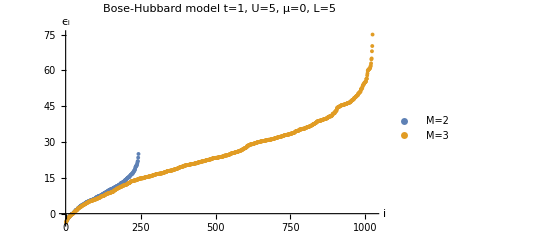

```mathematica
Block[{t=1,U=5,μ=0,M=Subscript[M, val],L=Subscript[L, val]},ListPlot[{Sort[Eigenvalues[Normal[N[Subscript[H, bose][t,U,μ,M,L]]]]],Sort[Eigenvalues[Normal[N[Subscript[H, bose][t,U,μ,M+1,L]]]]]},AxesLabel->{"i","ϵ_i"},PlotLabel->"Bose-Hubbard model\nt="<>ToString[t]<>", U="<>ToString[U]<>", μ="<>ToString[μ]<>", L="<>ToString[L],PlotLegends->{"M="<>ToString[M],"M="<>ToString[M+1]}]]
```

```mathematica
Subscript[β, val]=3/5;
```

```mathematica
(* example *)
Block[{t=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val]},MatrixExp[-β/2 N[Subscript[H, bose][t,U,μ,M,L]]]⟦1;;10,1;;10⟧]//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.09147 | 0. | 0.322637 | 0. | 0. | 0. | 0. | 0. | 0.0480369
0. | 0. | 0.283352 | 0. | 0.258831 | 0. | 0.0413406 | 0. | 0. | 0.
0. | 0.322637 | 0. | 1.13951 | 0. | 0. | 0. | 0. | 0. | 0.327419
0. | 0. | 0.258831 | 0. | 1.27348 | 0. | 0.27137 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.315388 | 0. | 0.175374 | 0. | 0.
0. | 0. | 0.0413406 | 0. | 0.27137 | 0. | 0.326233 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.175374 | 0. | 0.347617 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.069329 | 0.
0. | 0.0480369 | 0. | 0.327419 | 0. | 0. | 0. | 0. | 0. | 1.13986)

```mathematica
Subscript[A, op][n_,M_,L_]:=KroneckerProduct[SparseIdentityMatrix[(M+1)^(Floor[L/2]+n)],NumberOp[M],SparseIdentityMatrix[(M+1)^(L-Floor[L/2]-1-n)]]
```

```mathematica
Dimensions[Subscript[A, op][0,Subscript[M, val],Subscript[L, val]]]
```

{243,243}

```mathematica
(* example *)
Subscript[A, op][0,2,2]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2)

```mathematica
Z[H_,β_]:=Norm[MatrixExp[-β/2 H],"Frobenius"]^2
```

```mathematica
(* example *)
Block[{t=1,U=5,μ=0,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val]},Z[N[Subscript[H, bose][t,U,μ,M,L]],β]]
```

83.9712

```mathematica
Zref[H_,β_]:=Tr[MatrixExp[-β H]]
```

```mathematica
(* check *)
Block[{t=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],HB},HB=N[Subscript[H, bose][t,U,μ,M,L]];Abs[Z[HB,β]-Zref[HB,β]]]
```

2.84217×10^-14

```mathematica
(* Eq (9) in paper by Barthel, scheme A *)
χA[A_,B_,H_,β_,t_]:=1/Z[H,β] Tr[(MatrixExp[-β/2 H].MatrixExp[ⅈ t H]).B.(MatrixExp[-ⅈ t H].A.MatrixExp[-β/2 H])]
```

```mathematica
(* example *)
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],t=4},χA[N[Subscript[A, op][0,M,L]],N[Subscript[A, op][2,M,L]],N[Subscript[H, bose][tH,U,μ,M,L]],β,t]]
```

0.465163+0.00586079 ⅈ

```mathematica
(* alternative formulation corresponding to scheme C, see Eq (20) *)
χC[A_,B_,H_,β_,t_]:=Module[{tA=t/2,tB=t/2},1/Z[H,β] Tr[(MatrixExp[ⅈ tB H].MatrixExp[-β/2 H].B.MatrixExp[-ⅈ tB H]).(MatrixExp[-ⅈ tA H].A.MatrixExp[-β/2 H].MatrixExp[ⅈ tA H])]]
```

```mathematica
(* compare *)
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],t=4,HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Abs[χC[N[Subscript[A, op][0,M,L]],N[Subscript[A, op][2,M,L]],HB,β,t]-χA[N[Subscript[A, op][0,M,L]],N[Subscript[A, op][2,M,L]],HB,β,t]]]
```

4.45581×10^-16

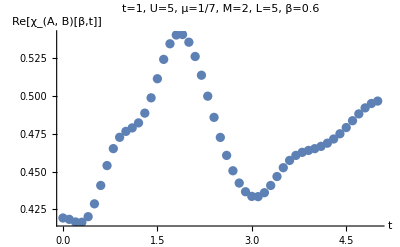

```mathematica
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val]},ListPlot[Re[Table[{t,χA[N[Subscript[A, op][0,M,L]],N[Subscript[A, op][2,M,L]],N[Subscript[H, bose][tH,U,μ,M,L]],β,t]},{t,0,5,0.1}]],AxesLabel->{"t","Re[χ_(A, B)[β,t]]"},PlotLabel->"t="<>ToString[tH]<>", U="<>ToString[U]<>", μ="<>ToString[InputForm[μ]]<>", M="<>ToString[M]<>", L="<>ToString[L]<>", β="<>ToString[N[β]]]]
```

### MPO operations

```mathematica
(* local Hamiltonian terms acting on neighboring lattice sites *)
h2[t_,U_,μ_,M_,L_]:=Module[{bd=SiteCreateOp[M],b=SiteAnnihilOp[M],S=U/2 NumberOp[M].(NumberOp[M]-IdentityMatrix[M+1])-μ NumberOp[M],SI,IS},SI=KroneckerProduct[S,IdentityMatrix[M+1]];IS=KroneckerProduct[IdentityMatrix[M+1],S];Table[-t(KroneckerProduct[bd,b]+KroneckerProduct[b,bd])+If[j==1,SI+1/2 IS,If[j<L-1,1/2(SI+IS),1/2 SI+IS]],{j,L-1}]]
```

```mathematica
(* check *)
Block[{t,U,μ,M=Subscript[M, val],L=Subscript[L, val]},Norm[Flatten[FullSimplify[Sum[KroneckerProduct[SparseIdentityMatrix[(M+1)^(l-1)],h2[t,U,μ,M,L]⟦l⟧,SparseIdentityMatrix[(M+1)^(L-l-1)]],{l,1,L-1}]-Subscript[H, bose][t,U,μ,M,L]]]]]
```

0

```mathematica
(* example *)
MatrixForm[#⟦1;;5,1;;5⟧]&/@h2[t,U,μ,Subscript[M, val],Subscript[L, val]]
```

{(0 | 0 | 0 | 0 | 0
0 | -μ/2 | 0 | -t | 0
0 | 0 | 1/2 (U-2 μ) | 0 | -√2 t
0 | -t | 0 | -μ | 0
0 | 0 | -√2 t | 0 | -(3 μ)/2),(0 | 0 | 0 | 0 | 0
0 | -μ/2 | 0 | -t | 0
0 | 0 | 1/2 (U-2 μ) | 0 | -√2 t
0 | -t | 0 | -μ/2 | 0
0 | 0 | -√2 t | 0 | -μ),(0 | 0 | 0 | 0 | 0
0 | -μ/2 | 0 | -t | 0
0 | 0 | 1/2 (U-2 μ) | 0 | -√2 t
0 | -t | 0 | -μ/2 | 0
0 | 0 | -√2 t | 0 | -μ),(0 | 0 | 0 | 0 | 0
0 | -μ | 0 | -t | 0
0 | 0 | U-2 μ | 0 | -√2 t
0 | -t | 0 | -μ/2 | 0
0 | 0 | -√2 t | 0 | -(3 μ)/2)}

```mathematica
(* MPO representing identity operation *)
Subscript[A, id]=Table[ArrayReshape[IdentityMatrix[Subscript[M, val]+1],{Subscript[M, val]+1,Subscript[M, val]+1,1,1}],{i,Subscript[L, val]}]
Dimensions[%]
```

{{{{{1}},{{0}},{{0}}},{{{0}},{{1}},{{0}}},{{{0}},{{0}},{{1}}}},{{{{1}},{{0}},{{0}}},{{{0}},{{1}},{{0}}},{{{0}},{{0}},{{1}}}},{{{{1}},{{0}},{{0}}},{{{0}},{{1}},{{0}}},{{{0}},{{0}},{{1}}}},{{{{1}},{{0}},{{0}}},{{{0}},{{1}},{{0}}},{{{0}},{{0}},{{1}}}},{{{{1}},{{0}},{{0}}},{{{0}},{{1}},{{0}}},{{{0}},{{0}},{{1}}}}}

{5,3,3,1,1}

```mathematica
(* check *)
Norm[MPOMergeFull[Subscript[A, id]]-IdentityMatrix[(Subscript[M, val]+1)^Subscript[L, val]]]
```

0

#### ⅇ^(-β H/2) MPO approximation

```mathematica
(* example *)
Block[{t=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],nsteps=20,tol=10^-12},MPOStrangStep[Subscript[A, id],N[h2[t,U,μ,M,L]],β/2 1/nsteps,tol]];
Dimensions/@%
```

{{3,3,1,9},{3,3,9,9},{3,3,9,9},{3,3,9,9},{3,3,9,1}}

```mathematica
(* example *)
Block[{t=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],nsteps=20,tol=10^-12},MPOSRKNb6Step[Subscript[A, id],N[h2[t,U,μ,M,L]],β/2 1/nsteps,tol]];
Dimensions/@%
```

{{3,3,1,9},{3,3,9,11},{3,3,11,11},{3,3,11,9},{3,3,9,1}}

```mathematica
(* compare *)
Block[{t=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],nsteps=40,tol=10^-15},Norm[MPOMergeFull[MPOStrangStep[Subscript[A, id],N[h2[t,U,μ,M,L]],β/2 1/nsteps,tol]]-MatrixExp[-β/2 1/nsteps N[Subscript[H, bose][t,U,μ,M,L]]]]]
```

2.69441×10^-6

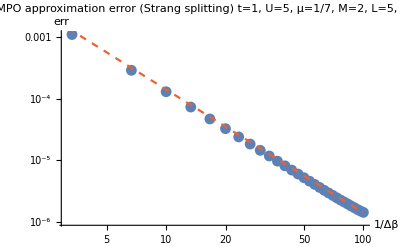

```mathematica
Block[{t=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],tol=10^-12,HB},HB=N[Subscript[H, bose][t,U,μ,M,L]];Show[ListLogLogPlot[Table[{nsteps/(β/2),1/Z[HB,β] Norm[MPOMergeFull[MPOEvolution[MPOStrangStep,Subscript[A, id],N[h2[t,U,μ,M,L]],β/2,nsteps,tol]]-MatrixExp[-β/2 HB]]},{nsteps,1,30}],AxesLabel->{"1/Δβ","err"},PlotLabel->"ⅇ^(-β H/2) MPO approximation error (Strang splitting)\nt="<>ToString[t]<>", U="<>ToString[U]<>", μ="<>ToString[InputForm[μ]]<>", M="<>ToString[M]<>", L="<>ToString[L]<>", β="<>ToString[N[β]]<>", tol=10^-12",PlotRange->All],LogLogPlot[0.014 invΔβ^-2,{invΔβ,1,100},PlotStyle->{ColorData[97][4],Dashed}]]]
```

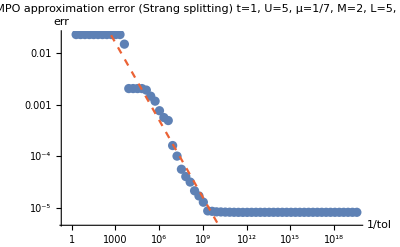

```mathematica
Block[{t=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],nsteps=12,tol,HB},HB=N[Subscript[H, bose][t,U,μ,M,L]];Show[ListLogLogPlot[Table[tol=2^-i;{1/tol,1/Z[HB,β] Norm[MPOMergeFull[MPOEvolution[MPOStrangStep,Subscript[A, id],N[h2[t,U,μ,M,L]],β/2,nsteps,tol]]-MatrixExp[-β/2 HB]]},{i,1,65}],AxesLabel->{"1/tol","err"},PlotLabel->"ⅇ^(-β H/2) MPO approximation error (Strang splitting)\nt="<>ToString[t]<>", U="<>ToString[U]<>", μ="<>ToString[InputForm[μ]]<>", M="<>ToString[M]<>", L="<>ToString[L]<>", β="<>ToString[N[β]]<>", Δβ="<>ToString[N[β/nsteps]]],LogLogPlot[0.5 invtol^(-1/2),{invtol,1,2^65},PlotStyle->{ColorData[97][4],Dashed}]]]
```

#### ⅇ^(-ⅈ t H) MPO approximation

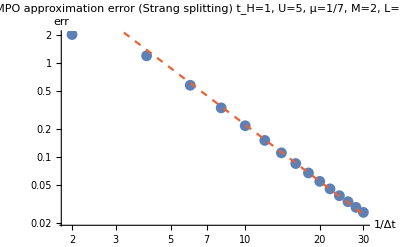

```mathematica
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],t=4,tol=10^-8,HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Show[ListLogLogPlot[Table[{nsteps/t,Norm[MPOMergeFull[MPOEvolution[MPOStrangStep,Subscript[A, id],N[h2[tH,U,μ,M,L]],ⅈ t,nsteps,tol]]-MatrixExp[-ⅈ t HB]]},{nsteps,8,120,8}],AxesLabel->{"1/Δt","err"},PlotLabel->"ⅇ^(-ⅈ t H) MPO approximation error (Strang splitting)\nt_H="<>ToString[tH]<>", U="<>ToString[U]<>", μ="<>ToString[InputForm[μ]]<>", M="<>ToString[M]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", tol=10^-8",PlotRange->All],LogLogPlot[22 invΔt^-2,{invΔt,1/10,30},PlotStyle->{ColorData[97][4],Dashed},PlotRange->All]]]
```

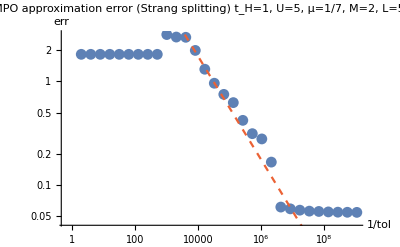

```mathematica
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],t=4,Δt=1/20,tol,HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Show[ListLogLogPlot[Table[tol=2^-i;{1/tol,Norm[MPOMergeFull[MPOEvolution[MPOStrangStep,Subscript[A, id],N[h2[tH,U,μ,M,L]],ⅈ t,t/Δt,tol]]-MatrixExp[-ⅈ t HB]]},{i,1,30}],AxesLabel->{"1/tol","err"},PlotLabel->"ⅇ^(-ⅈ t H) MPO approximation error (Strang splitting)\nt_H="<>ToString[tH]<>", U="<>ToString[U]<>", μ="<>ToString[InputForm[μ]]<>", M="<>ToString[M]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", Δt="<>ToString[N[Δt]]],LogLogPlot[175 invtol^(-1/2),{invtol,1,2^30},PlotStyle->{ColorData[97][4],Dashed}]]]
```

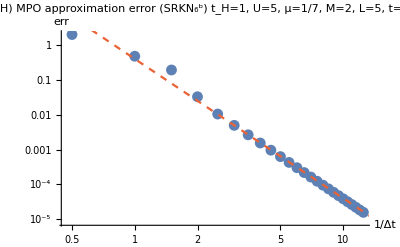

```mathematica
(* can reach smaller errors compared to Strang splitting *)
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],t=4,tol=10^-12,HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Show[ListLogLogPlot[Table[{nsteps/t,Norm[MPOMergeFull[MPOEvolution[MPOSRKNb6Step,Subscript[A, id],N[h2[tH,U,μ,M,L]],ⅈ t,nsteps,tol]]-MatrixExp[-ⅈ t HB]]},{nsteps,2,50,2}],AxesLabel->{"1/Δt","err"},PlotLabel->"ⅇ^(-ⅈ t H) MPO approximation error (SRKN_6^b)\nt_H="<>ToString[tH]<>", U="<>ToString[U]<>", μ="<>ToString[InputForm[μ]]<>", M="<>ToString[M]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", tol=10^-12",PlotRange->All],LogLogPlot[0.4 invΔt^-4,{invΔt,1/10,15},PlotStyle->{ColorData[97][4],Dashed}]]]
```

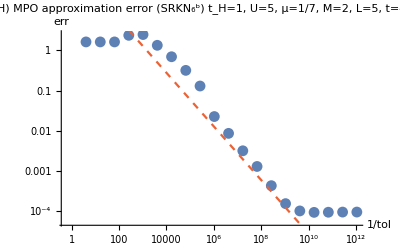

```mathematica
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],t=4,Δt=1/8,tol,HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Show[ListLogLogPlot[Table[tol=2^-i;{1/tol,Norm[MPOMergeFull[MPOEvolution[MPOSRKNb6Step,Subscript[A, id],N[h2[tH,U,μ,M,L]],ⅈ t,t/Δt,tol]]-MatrixExp[-ⅈ t HB]]},{i,2,40,2}],AxesLabel->{"1/tol","err"},PlotLabel->"ⅇ^(-ⅈ t H) MPO approximation error (SRKN_6^b)\nt_H="<>ToString[tH]<>", U="<>ToString[U]<>", μ="<>ToString[InputForm[μ]]<>", M="<>ToString[M]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", Δt="<>ToString[N[Δt]]],LogLogPlot[128 invtol^(-2/3),{invtol,1,2^50},PlotStyle->{ColorData[97][4],Dashed}]]]
```

#### ⅇ^(-ⅈ t H)X ⅇ^(ⅈ t H) MPO approximation

```mathematica
SeedRandom[42];
Subscript[A, rnd]=Block[{L=Subscript[L, val],M=Subscript[M, val],D=5,zmax},zmax=√2(1+ⅈ)/D;Table[If[j==1,RandomComplex[{-zmax,zmax},{M+1,M+1,1,D}],If[j<L,RandomComplex[{-zmax,zmax},{M+1,M+1,D,D}],RandomComplex[{-zmax,zmax},{M+1,M+1,D,1}]]],{j,L}]];
Dimensions[%]
```

{5,3,3}

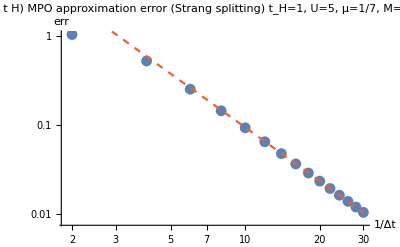

```mathematica
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],t=4,tol=10^-8,HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Show[ListLogLogPlot[Table[{nsteps/t,Norm[MPOMergeFull[MPOEvolution[MPOStrangLiouvilleStep,Subscript[A, rnd],N[h2[tH,U,μ,M,L]],ⅈ t,nsteps,tol]]-MatrixExp[-ⅈ t HB].MPOMergeFull[Subscript[A, rnd]].MatrixExp[ⅈ t HB]]},{nsteps,8,120,8}],AxesLabel->{"1/Δt","err"},PlotLabel->"ⅇ^(-ⅈ t H) X ⅇ^(ⅈ t H) MPO approximation error (Strang splitting)\nt_H="<>ToString[tH]<>", U="<>ToString[U]<>", μ="<>ToString[InputForm[μ]]<>", M="<>ToString[M]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", tol=10^-8",PlotRange->All],LogLogPlot[9.5 invΔt^-2,{invΔt,1/10,30},PlotStyle->{ColorData[97][4],Dashed},PlotRange->All]]]
```

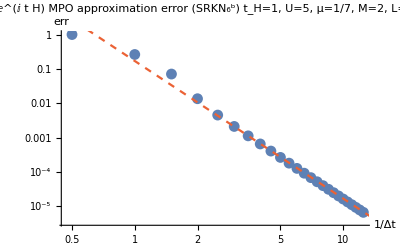

```mathematica
(* can reach smaller errors compared to Strang splitting *)
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],t=4,tol=10^-12,HB},HB=N[Subscript[H, bose][tH,U,μ,M,L]];Show[ListLogLogPlot[Table[{nsteps/t,Norm[MPOMergeFull[MPOEvolution[MPOSRKNb6LiouvilleStep,Subscript[A, rnd],N[h2[tH,U,μ,M,L]],ⅈ t,nsteps,tol]]-MatrixExp[-ⅈ t HB].MPOMergeFull[Subscript[A, rnd]].MatrixExp[ⅈ t HB]]},{nsteps,2,50,2}],AxesLabel->{"1/Δt","err"},PlotLabel->"ⅇ^(-ⅈ t H) X ⅇ^(ⅈ t H) MPO approximation error (SRKN_6^b)\nt_H="<>ToString[tH]<>", U="<>ToString[U]<>", μ="<>ToString[InputForm[μ]]<>", M="<>ToString[M]<>", L="<>ToString[L]<>", t="<>ToString[t]<>", tol=10^-12",PlotRange->All],LogLogPlot[0.17 invΔt^-4,{invΔt,1/10,15},PlotStyle->{ColorData[97][4],Dashed}]]]
```

```mathematica
(* virtual bond dimensions seem to be maxed out *)
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],t=1,Δt=1/8,tol=10^-8},Dimensions/@MPOEvolution[MPOSRKNb6LiouvilleStep,Subscript[A, rnd],N[h2[tH,U,μ,M,L]],ⅈ t,t/Δt,tol]]
```

{{3,3,1,9},{3,3,9,81},{3,3,81,81},{3,3,81,9},{3,3,9,1}}

#### Response function using MPO approximation

```mathematica
(* example *)
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],t=4},χA[N[Subscript[A, op][0,M,L]],N[Subscript[A, op][2,M,L]],N[Subscript[H, bose][tH,U,μ,M,L]],β,t]]
```

0.465163+0.00586079 ⅈ

```mathematica
(* compare (scheme A) *)
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],Δβ=1/50,t=4,Δt=1/8,tol=10^-12},Abs[MPOFrobeniusNorm[MPOEvolution[MPOStrangStep,Subscript[A, id],N[h2[tH,U,μ,M,L]],1/2 β,β/Δβ,tol]]^-2 MPOTraceProduct[MPOEvolution[MPOSRKNb6Step(*MPOStrangStep*),MPOEvolution[MPOSRKNb6Step,MPOSingleSiteTopUpdate[Subscript[A, id],5,NumberOp[M]],N[h2[tH,U,μ,M,L]],-ⅈ t,t/Δt,tol],N[h2[tH,U,μ,M,L]],1/2 β,β/Δβ,tol],MPOEvolution[MPOSRKNb6Step,MPOSingleSiteTopUpdate[MPOEvolution[MPOStrangStep,Subscript[A, id],N[h2[tH,U,μ,M,L]],1/2 β,β/Δβ,tol],3,NumberOp[M]],N[h2[tH,U,μ,M,L]],ⅈ t,t/Δt,tol]]-χA[N[Subscript[A, op][0,M,L]],N[Subscript[A, op][2,M,L]],N[Subscript[H, bose][tH,U,μ,M,L]],β,t]]]
```

1.98397×10^-6

```mathematica
(* compare (scheme C) *)
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],Δβ=1/50,ρβ,t=4,tA,tB,Δt=1/8,tol=10^-12},tA=t/2;tB=t/2;ρβ=MPOEvolution[MPOStrangStep,Subscript[A, id],N[h2[tH,U,μ,M,L]],1/2 β,β/Δβ,tol];Abs[MPOFrobeniusNorm[ρβ]^-2 MPOTraceProduct[MPOEvolution[MPOSRKNb6LiouvilleStep,MPOSingleSiteBottomUpdate[ρβ,5,NumberOp[M]],N[h2[tH,U,μ,M,L]],-ⅈ tB,tB/Δt,tol],MPOEvolution[MPOSRKNb6LiouvilleStep,MPOSingleSiteTopUpdate[ρβ,3,NumberOp[M]],N[h2[tH,U,μ,M,L]],ⅈ tA,tA/Δt,tol]]-χC[N[Subscript[A, op][0,M,L]],N[Subscript[A, op][2,M,L]],N[Subscript[H, bose][tH,U,μ,M,L]],β,t]]]
```

8.71663×10^-6

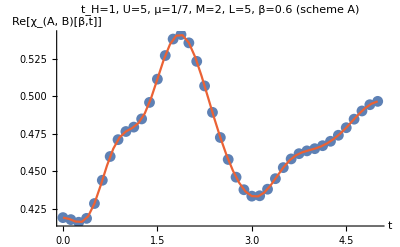

```mathematica
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],Δβ=1/20,ρβ,Δt=1/8,tol=10^-12},ρβ=MPOEvolution[MPOStrangStep,Subscript[A, id],N[h2[tH,U,μ,M,L]],1/2 β,β/Δβ,tol];Show[ListPlot[Re[Table[{n Δt,MPOFrobeniusNorm[ρβ]^-2 MPOTraceProduct[MPOEvolution[MPOSRKNb6Step,MPOEvolution[MPOSRKNb6Step,MPOSingleSiteTopUpdate[Subscript[A, id],5,NumberOp[M]],N[h2[tH,U,μ,M,L]],-ⅈ n Δt,n,tol],N[h2[tH,U,μ,M,L]],1/2 β,β/Δβ,tol],MPOEvolution[MPOSRKNb6Step,MPOSingleSiteTopUpdate[ρβ,3,NumberOp[M]],N[h2[tH,U,μ,M,L]],ⅈ n Δt,n,tol]]},{n,0,40}]],AxesLabel->{"t","Re[χ_(A, B)[β,t]]"},PlotLabel->"t_H="<>ToString[tH]<>", U="<>ToString[U]<>", μ="<>ToString[InputForm[μ]]<>", M="<>ToString[M]<>", L="<>ToString[L]<>", β="<>ToString[N[β]]<>" (scheme A)"],ListLinePlot[Re[Table[{t,χA[N[Subscript[A, op][0,M,L]],N[Subscript[A, op][2,M,L]],N[Subscript[H, bose][tH,U,μ,M,L]],β,t]},{t,0,5,0.1}]],PlotStyle->ColorData[97][4]]]]
```

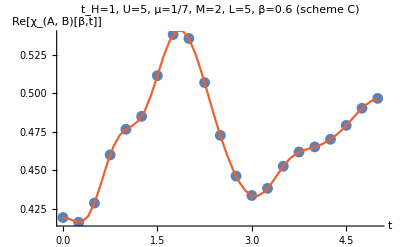

```mathematica
Block[{tH=1,U=5,μ=1/7,M=Subscript[M, val],L=Subscript[L, val],β=Subscript[β, val],Δβ=1/20,ρβ,tA,tB,Δt=1/8,tol=10^-12},ρβ=MPOEvolution[MPOStrangStep,Subscript[A, id],N[h2[tH,U,μ,M,L]],1/2 β,β/Δβ,tol];Show[ListPlot[Re[Table[{n Δt,tA=(n Δt)/2;tB=(n Δt)/2;MPOFrobeniusNorm[ρβ]^-2 MPOTraceProduct[MPOEvolution[MPOSRKNb6LiouvilleStep,MPOSingleSiteBottomUpdate[ρβ,5,NumberOp[M]],N[h2[tH,U,μ,M,L]],-ⅈ tB,tB/Δt,tol],MPOEvolution[MPOSRKNb6LiouvilleStep,MPOSingleSiteTopUpdate[ρβ,3,NumberOp[M]],N[h2[tH,U,μ,M,L]],ⅈ tA,tA/Δt,tol]]},{n,0,40,2}]],AxesLabel->{"t","Re[χ_(A, B)[β,t]]"},PlotLabel->"t_H="<>ToString[tH]<>", U="<>ToString[U]<>", μ="<>ToString[InputForm[μ]]<>", M="<>ToString[M]<>", L="<>ToString[L]<>", β="<>ToString[N[β]]<>" (scheme C)"],ListLinePlot[Re[Table[{t,χC[N[Subscript[A, op][0,M,L]],N[Subscript[A, op][2,M,L]],N[Subscript[H, bose][tH,U,μ,M,L]],β,t]},{t,0,5,0.1}]],PlotStyle->ColorData[97][4]]]]
```